/Users/prentner/Mathematica notebooks/Molecular QD

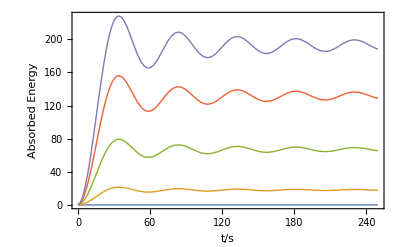

figures/abs.pdf

λ Sin[(π x)/tau]^2

{λ→1.0211,tau→61.7873}

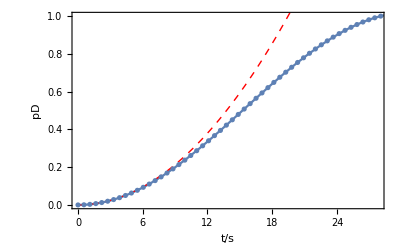

figures/pt.pdf

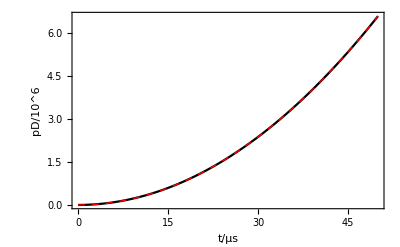

figures/pmt.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
MT=101;
NT = 101;
j=0;
abs = Table[0,{j,1,NT}];
t = Import["eigfun/cl2o2/simpar/long/absorbed_e_av_0.dat","Table"][[1;;NT,1]]*10^9;
Do[ str=StringJoin["eigfun/cl2o2/simpar/long/absorbed_e_av_",ToString[j-1],".dat"];tab=Import[str, "Table"][[1;;NT,2]];
abs[[j]] = Table[{t[[i]],tab[[i]]-tab[[1]]},{i,1,NT}],{j,1,MT}];

PlotAbs= ListLinePlot[Table[abs[[i]],{i,1,50,10}],PlotRange->{All,All},InterpolationOrder->2,
	PlotStyle->Thick,Frame->True,FrameLabel->{"t/s","Absorbed Energy"},Axes->{False,True},
	LabelStyle->Directive[FontFamily->"Times",FontSize->14]]

Export["figures/abs.pdf",PlotAbs]
absav = Table[{(j-1)*0.55,N[abs[[j]][[NT,2]]/abs[[52]][[NT,2]]]},{j,1,MT}];

model =λ*Sin[π*x/tau]^2

f=FindFit[absav,model,{{λ,500},{tau,50}},x]

pt=Show[Plot[Evaluate[model/.f],{x,0,55}],
	 Plot[λ*(π*x/tau)^2/.f,{x,0,20},PlotStyle->Directive[Red,Thick,Dashed]],
	 ListPlot[absav],PlotRange->{{0,27.8},{0,1.}},Frame->True,FrameLabel->{"t/s","pD"},
	 LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
Export["figures/pt.pdf",pt]
pmt=Show[Plot[{Evaluate[10^6*λ*(π*x/1000/tau)^2/.f],
	Evaluate[10^6*λ*Sin[(π*x/1000/tau)]^2/.f]},{x,0,50},
	PlotStyle->{Black,Directive[Red,Thick,Dashed]}],Frame->True,FrameLabel->{"t/μs","pD/10^6"},
	LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
Export["figures/pmt.pdf",pmt]
```